```mathematica
samples = {1.0,0.51014133245485715,0.32855345518295553,0.23965464220490629,0.1874587462281127,0.15275936628754372,0.12779936488716748,0.10885021600165262,0.093893031005485683,0.081735634548354058,0.071627695523531223,0.063072959919709473,0.055729749762765714,0.049354736236917045,0.043769495847585542,0.038839761284441117,0.03446208735290595,0.030555027012451937,0.027053151693236049,0.023902929886523788,0.021059870331963985,0.018486550579534015,0.016150940803513529,0.014020540887753865}
fit=Fit[samples,{1,1/r},r]
```

{1.,0.510141,0.328553,0.239655,0.187459,0.152759,0.127799,0.10885,0.093893,0.0817356,0.0716277,0.063073,0.0557297,0.0493547,0.0437695,0.0388398,0.0344621,0.030555,0.0270532,0.0239029,0.0210599,0.0184866,0.0161509,0.0140205}

-0.0239661+1.03659/r

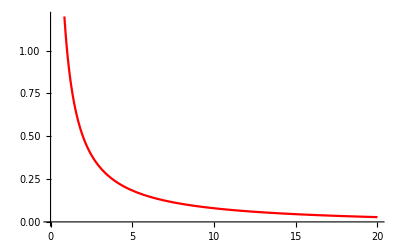

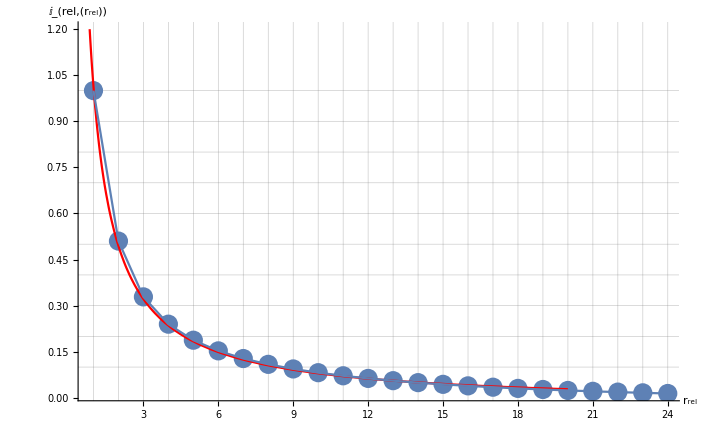

```mathematica
fp = Plot[fit,{r,0,20},PlotStyle->Red,PlotRange->{{0,20},{0,1.2}}]
lp=ListPlot[samples];
llp=ListPlot[samples,Joined->True];
Show[lp,fp,llp,AxesLabel->{Subscript[r, rel],Subscript[I, rel,"(r_rel)"]},GridLines->{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24},{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.0}},PlotRange->All]
```

```mathematica
FourierTransform[1/r,r,ω];
Simplify[%];
Cancel[%];
Abs[%]
```

√(π/2) Abs[Sign[ω]]

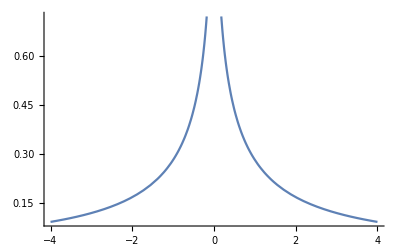

```mathematica
Plot[Abs[((0.+0.6266570686577502 ⅈ) Abs[ω])/ω-0.3989422804014327 CosIntegral[ω]+0.3989422804014327 Log[ω]-0.3989422804014327 Log[Abs[ω]]-(0.+0.3989422804014327 ⅈ) SinIntegral[ω]],{ω,-4,4}]
```

```mathematica
Abs[%]
```

√(π/2) Abs[Sign[ω]]

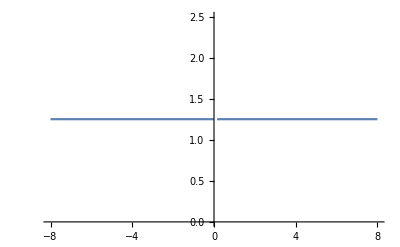

```mathematica
Plot[√(π/2) Abs[Sign[ω]],{ω,-8,8}]
```